# Lab 4: Manipulates, Phyllotaxis

## Kyle Perra - 7/9/2015

## Table and ListPlot

```mathematica
myTable=Table[i^3,{i,1,10}]
```

{1,8,27,64,125,216,343,512,729,1000}

```mathematica
myTable
```

{1,8,27,64,125,216,343,512,729,1000}

```mathematica
my2DTable=Table[i*j,{i,0,4},{j,0,4}]
```

{{0,0,0,0,0},{0,1,2,3,4},{0,2,4,6,8},{0,3,6,9,12},{0,4,8,12,16}}

```mathematica
Grid[my2DTable,Frame->All]
```

0 | 0 | 0 | 0 | 0
0 | 1 | 2 | 3 | 4
0 | 2 | 4 | 6 | 8
0 | 3 | 6 | 9 | 12
0 | 4 | 8 | 12 | 16

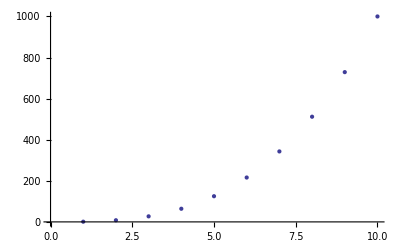

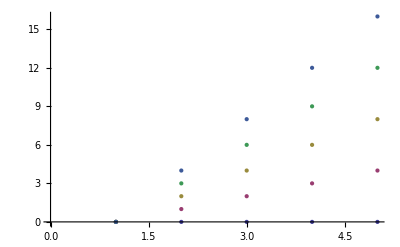

```mathematica
ListPlot[myTable]
ListPlot[my2DTable]
```

```mathematica
xyCoordinates=Table[Sqrt[i]*{Sin[i*137.5 Degree],Cos[i*137.5 Degree]},{i,0,10}]
```

{{0.,0.},{0.67559,-0.737277},{-1.40883,0.123257},{1.37413,1.05441},{-0.347296,-1.96962},{-1.20144,1.88588},{2.36603,-0.633975},{-2.34681,-1.22167},{0.967379,2.65785},{1.14805,-2.77164},{-2.866,1.33644}}

0. | 0.
0.67559 | -0.737277
-1.40883 | 0.123257
1.37413 | 1.05441
-0.347296 | -1.96962
-1.20144 | 1.88588
2.36603 | -0.633975
-2.34681 | -1.22167
0.967379 | 2.65785
1.14805 | -2.77164
-2.866 | 1.33644

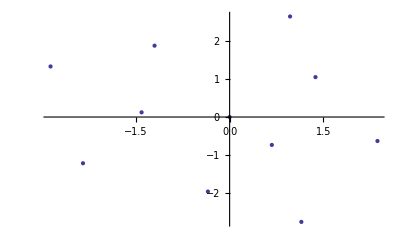

```mathematica
Grid[xyCoordinates,Frame->All]
ListPlot[xyCoordinates]
```

## Manipulate - Phyllotaxis

```mathematica
Manipulate[Graphics[{RGBColor[0,1.0,.5],Table[Circle[Sqrt[i]*{Sin[i(a Degree)],Cos[i(a Degree)]},size],{i,0,n}]}],{{n,100,"number of disks"},1,2000,Appearance->"Labeled"},{{size,.75,"radius of disks"},0.1,2,Appearance->"Labeled"},{{a,137.5,"angle"},0,180,Appearance->"Labeled"}]
```